```mathematica
(*Define constants*)k=1.0;
mass=1.0;
x0=5.0;
mu=0.20; (*Damping factor*)
dt=0.001;
time=15.0;

(*Define functions*)
PotentialEnergy[x_]:=0.5*k*x^2;
KineticEnergy[v_]:=0.5*mass*v^2;
Force[x_,v_]:=-k*x-mu*v;

(*Initialize variables*)
x=x0;
v=0.0;
data={};

(*Corrected loop*)
Do[pe=PotentialEnergy[x];
ke=KineticEnergy[v];
te=pe+ke;
a=Force[x,v]/mass;
x=x+v*dt+(a*(dt^2)/2);
v=v+a*dt;
AppendTo[data,{t,x,v,pe,ke,te}];,{t,0,time,dt}]

(*Export data to file*)
Export["Data.txt",data,"Table"]
```

Data.txt

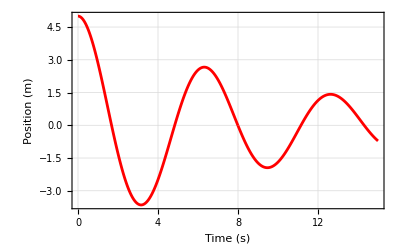

```mathematica
(*Import Data*)data=Import["Data.txt","Table"];

(*Extract Columns*)
timeValues=data[[All,1]];
xValues=data[[All,2]];
vValues=data[[All,3]];
peValues=data[[All,4]];
keValues=data[[All,5]];
teValues=data[[All,6]];

(*Plot Position vs Time*)
ListLinePlot[{Transpose[{timeValues,xValues}]},PlotStyle->{Red,Green},
Frame->True,FrameLabel->{"Time (s)","Position (m)"},
GridLines->Automatic,FrameTicks->All  ]
```

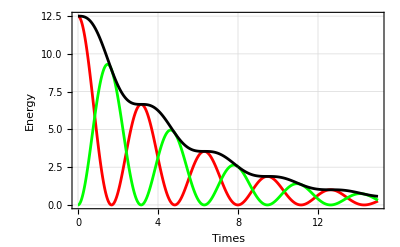

```mathematica
ListLinePlot[{Transpose[{timeValues,peValues}],Transpose[{timeValues,keValues}],Transpose[{timeValues,teValues}]},PlotStyle->{Red,Green,Black},
Frame->True,FrameLabel->{"Times"," Energy"},
GridLines->Automatic,FrameTicks->All  ]
```